Last modified on: Wednesday, July 11, 2018 at 1:46

Author Info

Pavlo Apisov

Matteo Salvarezza

Self-employed Android Developer

Poster Session Content

Generating Dynamic Piano Performances with Deep Learning

The idea behind the project is to generate sequence of notes that represent a musical performance.
We build a neural network that knows nothing about music and we try to teach it with thousands of songs given in MIDI format.

Add the most representative image of your project here. (We recommend just 1 image, if you add more, we will make a collage of the images.)

-Graphics-

Due to specific input data pre-processing introduced by Magenta team in their Performance-RNN model, we were able to train a model that generates musical sequences of 15-30 seconds.

Exploring possibilities of learning long-term structures in multi-instrumental music with using MusicVAE model made by Magenta team.

Note: Everything above this bar is your poster.Make sure it fits on a single page. "Preview Poster"

End of School Presentation Content

In addition to the poster content, include other content to present at the 2 minute presentation for end of school. Use the buttons below to add more sections."Add Header""Add Text""Add Code or Image"

Data

Approximately 4 500 classical songs in MIDI format.
MIDI carries event messages that specify musical notation, pitch, velocity(dynamic).

Preprocessing

-Graphics-

Results

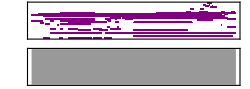
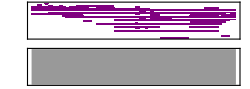
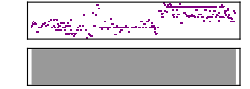

Note: Everything above this bar is in your 2 minute presentation. Make sure it fits on 2 slides. "Preview Presentation"

Detailed Project Notes

#### Main Results in Detail

After the first 10 rounds of training the model gives pretty musical performances.
The model starts overfitting during second session of training and tends to generate shorter in time performances.

#### Code

Constants

```mathematica
TimeShiftStepDuration = 10; (*ms*)
TimeMeasure = 1000 ;(* one second 1*)

NoteOnByte = "9";
NoteOffByte = "8";
MetaMessageByte = "F";

NoteOnEvent ="NoteOn";
NoteOffEvent = "NoteOff";
TimeShiftEvent = "TimeShift";
VelocityEvent = "VelocityChange";

MidiMaxValue = 127;
MidiNoteShift = 20; (*We use only 88 notes what is real piano range. So we need to substruct from MIDI number*)

NoteEventsLenght = 88;
TimeShiftsLenght = 100;
MaxTimeShift = (TimeShiftStepDuration/TimeMeasure ) * TimeShiftsLenght;
VelocitiesLenght = 34;
VelocityQuantizeCoef = VelocitiesLenght / MidiMaxValue;

NoteOnEventsEnd= NoteEventsLenght;
NoteOffEventsEnd = NoteEventsLenght * 2;
TimeShiftsEnd= NoteOffEventsEnd + TimeShiftsLenght;
VelocitiesEnd = TimeShiftsEnd + VelocitiesLenght;

OneHotSize = VelocitiesEnd;

OneHotEncoding = True;
```

Utilities

```mathematica
oneHotEncoding[position_Integer] := If[OneHotEncoding,UnitVector[OneHotSize, position], position]; (*Create one hot vector of vocabulary size*)

encodeNote[midiNote_Integer, isOn_]:=  Block[{note = midiNote - MidiNoteShift},
If[note <= 0,note = midiNote + 24(* Adding missing two octaves just in case *) - MidiNoteShift];

oneHotEncoding[If[isOn, note, NoteOnEventsEnd+ note]]
];

decodeNote[position_]:=  If[position < NoteEventsLenght, position + MidiNoteShift, position -  NoteEventsLenght+ MidiNoteShift];

encodeVelocity[velocity_Integer]:=  oneHotEncoding[TimeShiftsEnd + quantizedVelocity[velocity]];

quantizedVelocity[velocity_] := Floor[VelocityQuantizeCoef * velocity];

decodeVelocity[position_]:= Floor[N[(position - TimeShiftsEnd ) / VelocityQuantizeCoef]];

maxTimeShiftEncodings[count_]:= Table[oneHotEncoding[toTimeShiftIndex[MaxTimeShift]],{i,count }];

encodeTimeShift[duration_Real] :=If[duration≤MaxTimeShift,
(*Create only one vector with duration less or equal to one second *)
List[oneHotEncoding[toTimeShiftIndex[duration]]],

(*Otherwise create a list of one hot vectors*)
If[FractionalPart[duration]>0,
Join[
maxTimeShiftEncodings[IntegerPart[duration]],encodeTimeShift[FractionalPart[duration]]
],

maxTimeShiftEncodings[IntegerPart[duration]]
]
];

toTimeShiftIndex[duration_]:= Block[{index},
index = NoteOffEventsEnd + Round[(duration * TimeMeasure)/TimeShiftStepDuration];
If[index == NoteOffEventsEnd, index = NoteOffEventsEnd + 1, index]
];

decodeTimeShift[position_]:= N[((position - NoteOffEventsEnd) * TimeShiftStepDuration)/TimeMeasure]; (* return seconds*)

statusByte[note_] := note[[2,1]];(*status byte possition*)

velocityByte[note_] := note[[3,2]];(*velocity byte possition*)

noteByte[note_] := note[[3,1]];(*midi note byte possition*)

timeShiftByte[note_] := note[[1]] * secondsPerTick;(*time shift byte possition*)

noteEvents[raw_] :=  Select[#,
statusByte[#] == NoteOnByte 
|| statusByte[#] == NoteOffByte 
|| (timeShiftByte[#]>(TimeShiftStepDuration/TimeMeasure) && statusByte[#] ≠ MetaMessageByte)&
] &/@ raw;

trimTracks[noteEvents_] := Cases[noteEvents, Except[{}]];

getMidiEvents[raw_]:= trimTracks[noteEvents[raw]][[1]]; (* We are looking for a first track of midi tracks *)

rangeToNote=AssociationThread[Range[0,11]->{"C","C#","D","D#","E","F","F#","G","G#","A","A#","B"}];

noteToRange=AssociationMap[Reverse,rangeToNote];

idToNote[id_]:=With[{d=id-60},rangeToNote@Mod[d,12]<>ToString[Floor[d/12]+4]]
```

Encode midi sequence:

```mathematica
encode[track_] := Block[{lastVelocity = 0},
ClearAll[list];
Flatten[
	Map[
		Block[{list = {}},
			(* Add time shifts when needed *)
			If[timeShiftByte[#] > 0, list = Join[list, encodeTimeShift[timeShiftByte[#]]]];
			
			(* Procced with logic only if it a note event *)
			If[statusByte[#] == NoteOnByte || statusByte[#] == NoteOffByte,
			
				(* Add velocity if it's different from the last seen *)
				If[lastVelocity != quantizedVelocity[velocityByte[#]] && statusByte[#] == NoteOnByte,
				
					lastVelocity = quantizedVelocity[velocityByte[#]];
					list = Join[list, List[encodeVelocity[velocityByte[#]]]];
				];
			
				(* Add note event *)
				list = Join[list, List[encodeNote[noteByte[#], statusByte[#] == NoteOnByte]]];
			];
			
			(* Return encoded list*)
			list
		]&,
	track]
, 1]];
```

```mathematica
toEvents[encodings_] := Map[
	Block[{pos, type, value},
		pos = First@Flatten[Position[#, 1]];
		
		type = Which[
			pos ≤ NoteEventsLenght, NoteOnEvent,
			pos ≤ NoteOffEventsEnd, NoteOffEvent,
			pos ≤ TimeShiftsEnd, TimeShiftEvent,
			True, VelocityEvent
		];
		
		value = Switch[type,
			NoteOnEvent, decodeNote[pos],
			NoteOffEvent, decodeNote[pos],
			TimeShiftEvent, decodeTimeShift[pos],
			VelocityEvent, decodeVelocity[pos]
		];
				
		type -> value
	]&,
encodings];
```

Decode one-hot sequence:

```mathematica
toSound[encodings_] := SortBy[Flatten[Block[{notes, events}, 
	events = toEvents[encodings];
	notes = Intersection[Cases[events, HoldPattern["NoteOn" -> note_] :> note], Cases[events, HoldPattern["NoteOff" -> note_] :> note]];
	
	Map[
		Block[{note = #, ons, offs, onOffs, durations, starts, velocities},
			ons = Flatten[Position[events, NoteOnEvent -> note]];
			offs = Flatten[Position[events, NoteOffEvent -> note]];
			
			Do[
			If[i≤ Length@offs,
				If[ons[[i]]> offs[[i]], offs = Drop[offs, 1]];
			]
			,{i, Length@ons}];
			
			If[Length@ons < Length@offs, offs = Take[offs, Length@ons], ons = Take[ons, Length@offs]];
			
			onOffs = Transpose @ {ons, offs};
			durations = Total @ Cases[events[[First@# + 1 ;; Last@# - 1]], HoldPattern["TimeShift" -> duration_] :> duration] &/@ onOffs;
			starts = Total @ Cases[Take[events, First@#], HoldPattern["TimeShift" -> start_] :> start] &/@ onOffs;
			velocities = Last @ Cases[Take[events, First@#], HoldPattern["VelocityChange" -> velocity_] :> velocity] &/@ onOffs;
			Table[
				Block[{start = starts[[i]], duration = durations[[i]], velocity = velocities[[i]]},
					SoundNote[idToNote@note, {start, start + duration}, SoundVolume -> velocity]
				],
			{i, Length@starts}]
		] &,
	notes]
]], #[[2,1]]&];
```

```mathematica
getHalfMinutesPositions[track_]:=Block[{positions ={},time =0},
Do[
time = time + track[[i]][[1]] * secondsPerTick;
If[time > 30, positions= Append[positions,i]; time =0;],

{i, Length@track}];

positions
]
```

```mathematica
encodeTrack[path_] := Block[{encodings},
	{raw, header} = Import[path, #]& /@ {"RawData", "Header"};
	tempos = Cases[Flatten[raw], HoldPattern["SetTempo" -> tempo_] :> tempo];
	microsecondsPerBeat = If[Length@tempos > 0, First[tempos], 500000];
	
	ticksPerBeat = First@Cases[header,HoldPattern["TimeDivision"->x_] :> x];
	secondsPerTick = (microsecondsPerBeat/ticksPerBeat) * 10^-6.;
	
	encodings = Partition[encode[getMidiEvents[raw]], 500];
	Print[StringJoin["Encoded: ", path]];
	
	encodings
];
```

Provide one of:

Link to the GitHub

Explicit code

#### Written Content / Lesson Plans

#### Conclusions in Detail

#### All Visualizations

```mathematica
30 rounds of traning
```

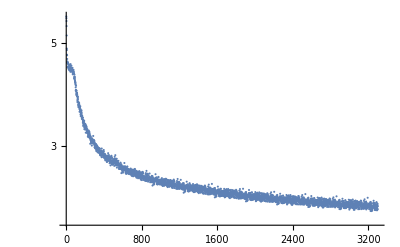

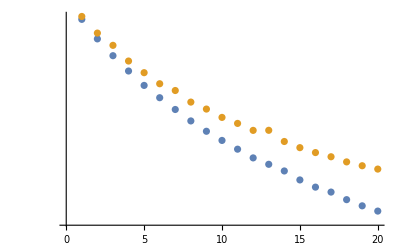

#### Data Sources Links/References

#### Future Directions

#### Background Info Links/References

#### Keywords

Provide keywords as items

< keyword 1 >

< keyword 2 >

#### Other information